# BigData Optimal Tax: Life-Cycle

This notebook takes the basic life cycle model and examines what happens for many alternative combinations of capital and labor tax rates.

```mathematica
x=0; Remove["Global`*"];
```

Define the main life-cycle constants, the utility function, and the age-wage path.

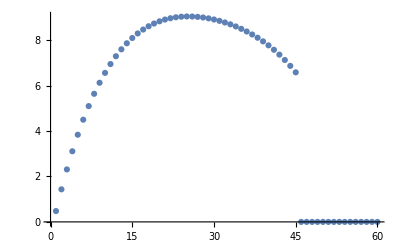

```mathematica
T=60;Tret=45;
r=0.1;R=1 + r; 
β=.95;
u[c_,l_] :=c^(1-γ)/(1-γ)-B l^(1+η)/(1+η)
Clear[w];
(* Specify age-wage path*)
Do[w[t]=-36.9994+3.52022(t+17)-.101878(t+17)^2+.00134816(t+17)^3-7.06233*10^-6(t+17)^4,{t,1,Tret}];
wagelist=Table[If[i≤ Tret,w[i],0],{i,T}];
ListPlot[wagelist]
```

We define the basic optimization problem.

```mathematica
Tax[capInc_,labInc_]:=τK (R-1) capInc   +τL labInc;
PVrevL:= Sum[τL w[t] l[t] R^(-t+1),{t,1,Tret}] ;
PVrevK:= Sum[τK (R-1) a[t] R^(-t+1),{t,1,T}] ;
PVrevC:= Sum[τC c[t] R^(-t+1),{t,1,T}] ;
```

```mathematica
obj := Sum[β^(t-1) u[c[t],l[t]],{t,1,T}];
(*Define Budget Constraints*)
bc1:=Table[(R  a[t]+w[t] l[t]-c[t]-Tax[ a[t],w[t] l[t]])-a[t+1]≥ 0,{t,1,T}];
(*Define Control variables*)
varsc:=Table[c[t],{t,1,T}];
varsl:=Table[l[t],{t,1,Tret}];
varsa:=Table[a[t],{t,2,T+1}];
vars:=Union[varsc,varsl,varsa];
(*Define bound Constraints*)
bcaT:={a[T+1]≥ 0};
abnds:=Table[a[t]≥ amin,{t,2,T}];
constraints1:=Union[bc1,bcaT,abnds];
lbndsc:=Table[c[t]≥ 0.0001,{t,1,T}];
lbndsl:=Thread[varsl≥0]; 
lbnds:=Union[lbndsc,lbndsl];
(*Collect all constraints*)
constraints:=Union[constraints1,lbnds];
```

```mathematica
(*Set initial guess for all variables to be 1; probably not a feasible point but better than letting them be zero.*)
varsinit=Table[{vars[[i]],1},{i,Length[vars]}];
```

This is the command which takes as input the tax rates, the borrowing constraints, and preference parameters, and outputs the individuals utility and taxes paid.

NOTE: This is a very simple problem. One should think of f[----] as a black box because it will often be a substantive computation on its own. In this notebook I do nothing that relies on special features of this problem. I use this problem because it is fast to compute, and it allows me to demonstrate the general concept of computing a Pareto frontier.

```mathematica
f[τK0_,τL0_,amin0_,γ0_,η0_,B0_]:=
Block[{a,c,l,utility,PVrevK0,PVrevL0,τK=τK0,τL=τL0,amin=amin0,γ=γ0,η=η0,B=B0},
(*Define border conditions particular to the problem*)
a[1]=0;
Do[ l[i]=0,{i,Tret+1,T}];
{utility,sol}=FindMaximum[{obj,constraints}, varsinit];
PVrevK0=PVrevK/.sol;PVrevL0=PVrevL/.sol;
{utility,PVrevK0+PVrevL0, PVrevK0,PVrevL0,τK,τL}
]
```

```mathematica
varsinit
```

{{a[2],1},{a[3],1},{a[4],1},{a[5],1},{a[6],1},{a[7],1},{a[8],1},{a[9],1},{a[10],1},{a[11],1},{a[12],1},{a[13],1},{a[14],1},{a[15],1},{a[16],1},{a[17],1},{a[18],1},{a[19],1},{a[20],1},{a[21],1},{a[22],1},{a[23],1},{a[24],1},{a[25],1},{a[26],1},{a[27],1},{a[28],1},{a[29],1},{a[30],1},{a[31],1},{a[32],1},{a[33],1},{a[34],1},{a[35],1},{a[36],1},{a[37],1},{a[38],1},{a[39],1},{a[40],1},{a[41],1},{a[42],1},{a[43],1},{a[44],1},{a[45],1},{a[46],1},{a[47],1},{a[48],1},{a[49],1},{a[50],1},{a[51],1},{a[52],1},{a[53],1},{a[54],1},{a[55],1},{a[56],1},{a[57],1},{a[58],1},{a[59],1},{a[60],1},{a[61],1},{c[1],1},{c[2],1},{c[3],1},{c[4],1},{c[5],1},{c[6],1},{c[7],1},{c[8],1},{c[9],1},{c[10],1},{c[11],1},{c[12],1},{c[13],1},{c[14],1},{c[15],1},{c[16],1},{c[17],1},{c[18],1},{c[19],1},{c[20],1},{c[21],1},{c[22],1},{c[23],1},{c[24],1},{c[25],1},{c[26],1},{c[27],1},{c[28],1},{c[29],1},{c[30],1},{c[31],1},{c[32],1},{c[33],1},{c[34],1},{c[35],1},{c[36],1},{c[37],1},{c[38],1},{c[39],1},{c[40],1},{c[41],1},{c[42],1},{c[43],1},{c[44],1},{c[45],1},{c[46],1},{c[47],1},{c[48],1},{c[49],1},{c[50],1},{c[51],1},{c[52],1},{c[53],1},{c[54],1},{c[55],1},{c[56],1},{c[57],1},{c[58],1},{c[59],1},{c[60],1},{l[1],1},{l[2],1},{l[3],1},{l[4],1},{l[5],1},{l[6],1},{l[7],1},{l[8],1},{l[9],1},{l[10],1},{l[11],1},{l[12],1},{l[13],1},{l[14],1},{l[15],1},{l[16],1},{l[17],1},{l[18],1},{l[19],1},{l[20],1},{l[21],1},{l[22],1},{l[23],1},{l[24],1},{l[25],1},{l[26],1},{l[27],1},{l[28],1},{l[29],1},{l[30],1},{l[31],1},{l[32],1},{l[33],1},{l[34],1},{l[35],1},{l[36],1},{l[37],1},{l[38],1},{l[39],1},{l[40],1},{l[41],1},{l[42],1},{l[43],1},{l[44],1},{l[45],1}}

Here is a simple example

```mathematica
f[.4,.5,-3000,0.5,1,1]//Timing
```

{1.19558,{62.7419,39.3704,-4.45625,43.8267,0.4,0.5}}

## Create Database

Build your database (or import it if already built)

```mathematica
gamlist={1/2};
etalist={1};
```

```mathematica
tkmax=0.4; tlmax=0.4;
```

```mathematica
dtk=0.005; dtl=0.005;
```

```mathematica
ntk=tkmax/dtk+1
ntl=tlmax/dtl + 1
```

81.

81.

We next evaluate many combinations of taxes for different preferences

{tk, 0, .50, .05} ({tl, 0, .50, .05}) says that we look at tk (tl) beginning with 0 and increasing to 0.50 in steps of 0.05

{aamin,{0}} says we impose a zero lower bound on assets (meaning no borrowing allowed)

{gam,gamlist} and {eeta,etalist} means that gam is drawn from gamlist and eeta is drawn from etalist

In this version, we allow borrowing:

```mathematica
data=ParallelTable[f[tk,tl,aamin,gam,eeta,n],{tk,0,tkmax,dtk},{tl,0,tlmax,dtl},{aamin,{0}},{gam,gamlist},{eeta,etalist},{n,{1}}];//AbsoluteTiming
```

{57.0384,Null}

```mathematica
time=%[[1]];
```

tmp is the number of cases. We compute how much time is spent on each example

```mathematica
numcases=Length[gamlist] Length[etalist] ntk ntl
numcases/time
```

6561.

115.028

output data

```mathematica
data>> dataoutMay2;
```

Next, we read the file

```mathematica
Clear[data]
data=<<dataoutMay2;
```

## The Pareto frontier - tables

In this notebook we care about utility versus revenue. I look forward to higher-dimensional frontiers.

Define Pareto function and Pareto frontier

Function h receives:
	Data in from database of cases
	Target revenue
	Indices - γind and ηind - indicating preference parameters

Function h outputs the optimal element for that revenue, and the policies that produced that outcome.

```mathematica
h[data_,revenue_, alimind_,γind_,ηind_]:=Module[
{dataflat,util,comb},
dataflat=Flatten[data[[All,All,alimind,γind,ηind,1]],1];
util=Max[Select[dataflat,#[[2]]≥revenue&][[All,1]]];
comb=Select[dataflat,#[[1]]==util&]
]
```

```mathematica
casesprefs=Table[{gamlist[[gam]],etalist[[eeta]]},{gam,1,Length[gamlist]},{eeta,1,Length[gamlist]}];
casesprefs=Flatten[casesprefs,1];
```

```mathematica
cases=Table[{1,gam,eeta},{gam,1,Length[gamlist]},{eeta,1,Length[gamlist]}];
cases=Flatten[cases,1];
```

```mathematica
numcases=Length[cases];
count=0;
```

```mathematica
outcmd:= (count=count+1;
{i,j,k}=cases[[count]];
Print["gamma = ",casesprefs[[count]][[1]],",   eta = ",casesprefs[[count]][[2]]]
maxrev=Transpose[Flatten[data[[All,All,i,j,k,1]],1]][[2]]//Max;
tb=Table[h[data,rev,i,j,k][[1]],{rev,0,0.99 maxrev ,0.04 maxrev}];
TableForm[tb,TableHeadings->{{},{"util","revtot","revk","revl","tk","tl"}}])
```

```mathematica
outcmdold:= (
count=count+1;
{i,j,k}=cases[[count]];
Print["gamma = ",casesprefs[[count]][[1]],",   eta = ",casesprefs[[count]][[2]]]
maxrev=Transpose[Flatten[data[[All,All,i,j,k,1]],1]][[2]]//Max;
Table[h[data,rev,i,j,k][[1]],{rev,0,0.96 maxrev ,0.02 maxrev}]//TableForm)
```

```mathematica
outcmd
```

gamma = 1/2,   eta = 1

| util | revtot | revk | revl | tk | tl
 | 116.907 | 0. | 0. | 0. | 0. | 0.
 | 115.735 | 1.87522 | 0. | 1.87522 | 0. | 0.015
 | 114.443 | 3.82448 | 3.20302 | 0.621466 | 0.02 | 0.005
 | 113.25 | 5.75684 | 0.810358 | 4.94649 | 0.005 | 0.04
 | 112.068 | 7.55933 | 0.79352 | 6.76581 | 0.005 | 0.055
 | 110.774 | 9.48339 | 1.53401 | 7.94938 | 0.01 | 0.065
 | 109.586 | 11.2325 | 1.50128 | 9.73125 | 0.01 | 0.08
 | 108.223 | 13.1382 | 2.86433 | 10.2738 | 0.02 | 0.085
 | 106.95 | 15.022 | 0. | 15.022 | 0. | 0.125
 | 105.579 | 16.915 | 1.39349 | 15.5215 | 0.01 | 0.13
 | 104.078 | 18.9683 | 0. | 18.9683 | 0. | 0.16
 | 102.836 | 20.6224 | 0. | 20.6224 | 0. | 0.175
 | 101.167 | 22.792 | 0. | 22.792 | 0. | 0.195
 | 99.9062 | 24.3918 | 0. | 24.3918 | 0. | 0.21
 | 98.2128 | 26.4875 | 0. | 26.4875 | 0. | 0.23
 | 96.5047 | 28.5393 | 0. | 28.5393 | 0. | 0.25
 | 95.2136 | 30.0486 | 0. | 30.0486 | 0. | 0.265
 | 93.5327 | 31.8573 | 2.64422 | 29.2131 | 0.025 | 0.26
 | 91.8398 | 33.7236 | 2.54936 | 31.1742 | 0.025 | 0.28
 | 90.0941 | 35.6208 | 1.98507 | 33.6357 | 0.02 | 0.305
 | 88.3096 | 37.4792 | 1.44643 | 36.0327 | 0.015 | 0.33
 | 86.4262 | 39.3623 | 0.471942 | 38.8904 | 0.005 | 0.36
 | 84.3853 | 41.2316 | 1.74147 | 39.4901 | 0.02 | 0.37
 | 82.4136 | 43.044 | 0.849076 | 42.1949 | 0.01 | 0.4
 | 79.6303 | 45.0575 | 3.61092 | 41.4466 | 0.05 | 0.4

## The Pareto frontier - graphs

### Plot all data

We plot all the data points in revenue-utility space. This helps us see where the good points are. I also use colors to indicate the policies.

plot

```mathematica
tmax=Max[tkmax,tlmax]
```

0.4

```mathematica
plot[alimind_,γind_,ηind_]:=Module[

{alimi=alimind,γi=γind,ηi=ηind,Βi=1,dots,colorF,gra1,gra2,plotLegend,leg},

dots=Flatten[data[[All,All,alimi,γi,ηi,Βi]],1];

colorF=Blend[{{0,Green},{tmax,Red}},#]&;

gra1=Graphics[
{{colorF[#5],Tooltip[Point[{#2,#1}],{#5,#6}]}&@@@dots,Text["τK",{Max[dots[[All,2]]]/2,Max[dots[[1,1]]]},{0,-1}]},
Frame->{{True,False},{True,False}}, 
PlotRange->All,
AxesOrigin->{0,0},
FrameLabel-> {"Total Tax Revenue","Consumer Utility"},
ImageSize->Medium,
AxesOrigin-> {0,0}];

gra2=Graphics[{{colorF[#6],Tooltip[Point[{#2,#1}],{#5,#6}]}&@@@dots,Text["τL",{Max[dots[[All,2]]]/2,Max[dots[[1,1]]]},{0,-1}]},Frame->{{True,False},{True,False}}, PlotRange->All,AxesOrigin->{0,0},FrameLabel->{"Total Tax Revenue","Consumer Utility"},ImageSize->Medium,AxesOrigin-> {0,0}];

plotLegend[{min_,max_},n_,col_]:=Graphics[MapIndexed[{{col[#1],Rectangle[{0,#2[[1]]-1},{1,#2[[1]]}]},{Black,Text[NumberForm[N@#1,{4,2}],{4,#2[[1]]-.5},{1,0}]}}&,Rescale[Range[n],{1,n},{min,max}]],Frame->True,FrameTicks->None,PlotRangePadding->.5];

leg=plotLegend[{0,0.8},20,colorF];
Grid[{{Row[{"γ= ",2^(γi-2), ", η= ",Piecewise[{{10,ηi==4},{5,ηi==3}},ηi ] , ", Borrowinglimit= ",Piecewise[{{-(alimi-1)*10,alimi<4},{-50,alimi==4}},-∞]}],SpanFromLeft},{gra1,gra2,leg}},ItemSize->Automatic]
]
```

```mathematica
count=0;
```

```mathematica
prntcmd:=(
count=count+1;
{i,j,k}=cases[[count]];
Print["gamma = ",casesprefs[[count]][[1]],",   eta = ",casesprefs[[count]][[2]]];
plot[i,j,k])
```

Each plot is a point in utility-revenue space. The left one uses color to indicate the size of the capital income tax; the right one does so for the labor income tax.
Note that there are some red points in the τL graph that are on the frontier, but the red points in the τK graph are all inferior.

gamma = 1/2,   eta = 1

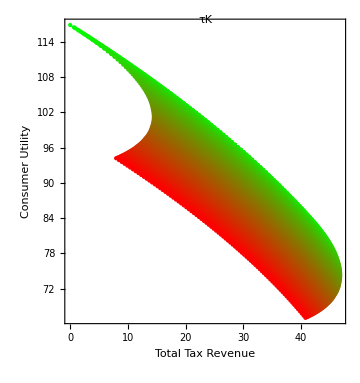
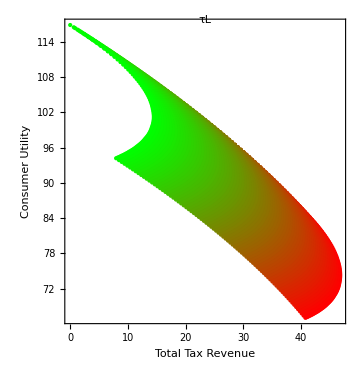
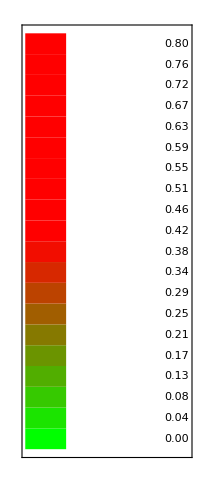
γ= 1/2, η= 1, Borrowinglimit= 0 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
prntcmd
```